# Coupled Exponentials & Logarithms

## Graphic of Coupled Exponential

Graph shows curves from linear (κ = -0.5) to exponential (κ = 0)

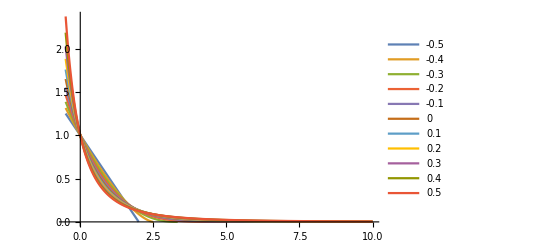

```mathematica
CouplingValues = {-0.5,-0.4,-0.3,-0.2,-0.1,0, 0.1,0.2,0.3,0.4,0.5};
Plot[CoupledExponential[x,#]^-1&/@CouplingValues//Evaluate,{x,-0.5,10},PlotLegends->CouplingValues,PlotRange->Full]
```

The curves are produced by the Coupled Exponential Function
	(1+κ x)^(-(1 + κ)/κ)

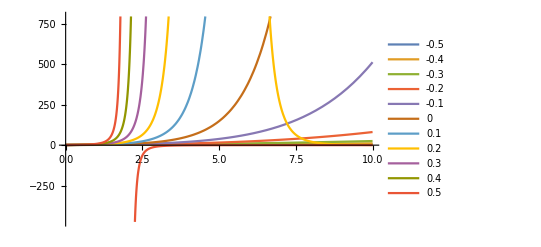

```mathematica
CouplingValues = {-0.5,-0.4,-0.3,-0.2,-0.1,0, 0.1,0.2,0.3,0.4,0.5};
Plot[CoupledExponential[-x,#]^-1&/@CouplingValues//Evaluate,{x,0,10},PlotLegends->CouplingValues]
```

The curves are produced by the Coupled Exponential Function
	(1-κ x)^((1 + κ)/-κ)

## Graphic of Coupled Logarithm

Graph shows curves from linear to logarithmic

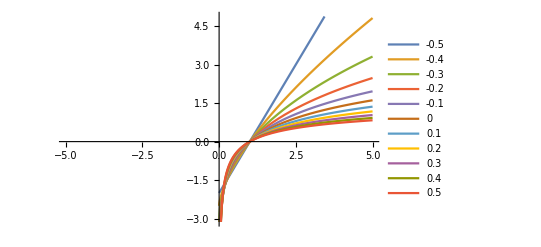

```mathematica
CouplingValues = {-0.5,-0.4,-0.3,-0.2,-0.1,0, 0.1,0.2,0.3,0.4,0.5};
Quiet[Plot[
-CoupledLogarithm[x^-1,#]&/@CouplingValues//Evaluate,{x,-5,5},
PlotLegends->CouplingValues],
{Power::infy}]
```

The curves are produced by the Coupled Logarithmic Function
	1/(- κ)(x^((- κ)/(1+ κ))-1)

## Coupled Normal Distribution

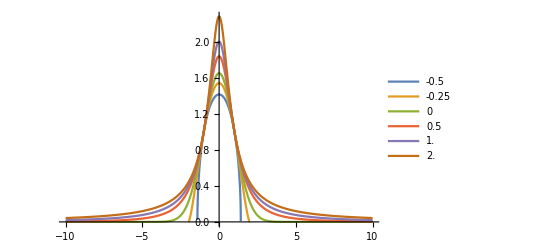

```mathematica
CouplingValues = {-0.5,-0.25,0,0.5,1.0,2.0};
Quiet[Plot[
PDF[CoupledNormalDistribution[0,1,#],{x}]/PDF[CoupledNormalDistribution[0,1,#],{1}]&/@CouplingValues//Evaluate,{x,-10,10},
PlotLegends->CouplingValues,
PlotRange->Full],
{Power::infy}]
```

## Coupled Gaussian is Scale-Free as σ → 0

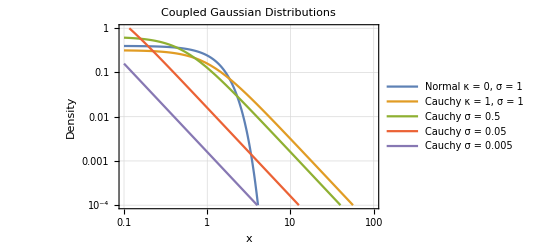

```mathematica
Parameters={{1,1,0.5,0.05,0.005},{0,1,1,1,1}};
Quiet[LogLogPlot[MapThread[
PDF[CoupledNormalDistribution[0,#1,#2],{x}]&,Parameters]//Evaluate,{x,0.1,100},
PlotLegends->{"Normal κ = 0, σ = 1", "Cauchy κ = 1, σ = 1","Cauchy σ = 0.5",
"Cauchy σ = 0.05","Cauchy σ = 0.005"},
LabelStyle->Directive[Gray,Smaller],
PlotRange->{{0.1,100},{10^-4,1}},
PlotTheme->{"Detailed"},
FrameLabel->{"x","Density"},
PlotLabel->"Coupled Gaussian Distributions"],
{Power::infy}]
```